```mathematica
(* Mersenne Prime *)
m=2^13-1;
Print["The factors of 8191 are ",FactorInteger[m]]  (* verifying m prime *)
a=PrimitiveRootList[m][[1]];   (* finding primitive root for a *)
x0=2; 
xvec={x0};

(* Construct sequence *)
While[Length[xvec]<m-1 ,
AppendTo[xvec,Mod[a*x0,m]];
x0=a*x0;
];

(* Verifying that xvec has 8190 unique entries between 1 and 8190 *)
Print["xvec has ", Length[Union[xvec]] " unique elements"] 
Print["The maxium element of xvec is ",Max[xvec]]
Print["The minimum element of xvec is " ,Min[xvec]]
(* divide by length m *)
xvec=N[xvec/m,6];
```

The factors of 8191 are {{8191,1}}

xvec has 8190  unique elements

The maxium element of xvec is 8190

The minimum element of xvec is 1

```mathematica
f[x_]:=CDF[NormalDistribution[0,1],x];

xval={};
For[i=1,i≤Length[xvec],++i,
AppendTo[xval,Solve[f[x]==xvec[[i]]]]
];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

```mathematica
xval1={};
For[i=1,i≤Length[xval],++i,
If[xval[[i]]≠{},
AppendTo[xval1,xval[[i]]]
];
]; 

xnorms={};
For[i=1,i≤Length[xval1],++i,
AppendTo[xnorms,x/.xval1[[i]][[1]]]
];
xnorms;
Length[xnorms]
```

7731

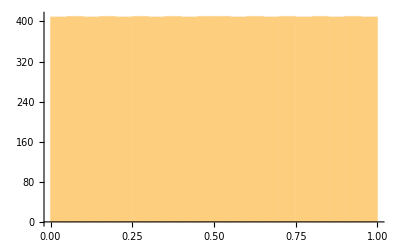

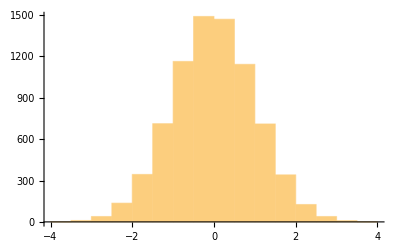

```mathematica
Histogram[xvec]
Histogram[xnorms]
```